```mathematica
β=2;ω0=2*Pi;
```

```mathematica
G[ω_]:=ω0^2/((ω0^2 - ω^2)+I*β*ω);
```

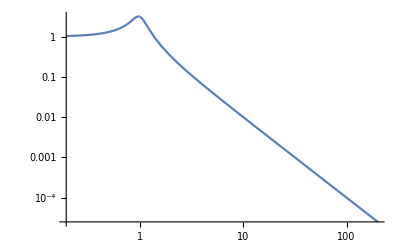

```mathematica
LogLogPlot[Abs[G[a*ω0]],{a,0,200}]
```

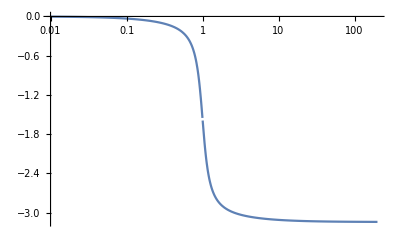

```mathematica
LogLinearPlot[Arg[G[a*ω0]],{a,0.01,200}]
```

Setting Ki, Kp relative to Kd as below basically turns the system (DDSHO, which is 2nd order) into a low-pass filter (first-order). The resonance (pole of K[omega]*G[omega]) is removed. K[omega]*G[omega] is now -i*I/omega.

```mathematica
Kd=1;Kp=β*Kd;Ki=ω0^2*Kd;
```

```mathematica
K[ω_]:=Kp-I*Ki/ω+I*Kd*ω;F[ω_]:=G[ω]*K[ω]/(1+G[ω]*K[ω]);
```

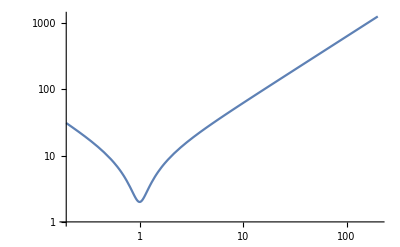

```mathematica
LogLogPlot[Abs[K[a*ω0]],{a,0,200}]
```

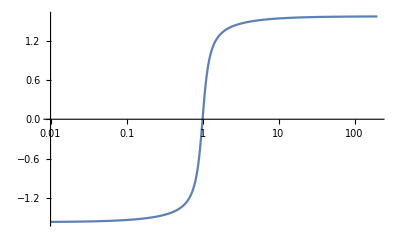

```mathematica
LogLinearPlot[Arg[K[a*ω0]],{a,0.01,200},PlotRange->Full]
```

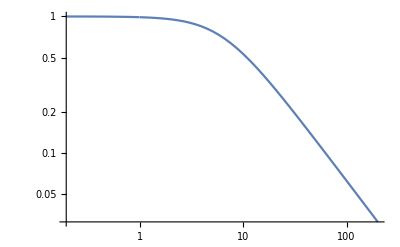

```mathematica
LogLogPlot[Abs[F[a*ω0]],{a,0,200}]
```

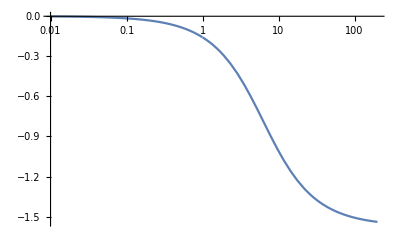

```mathematica
LogLinearPlot[Arg[F[a*ω0]],{a,0.01,200},PlotRange->Full]
```

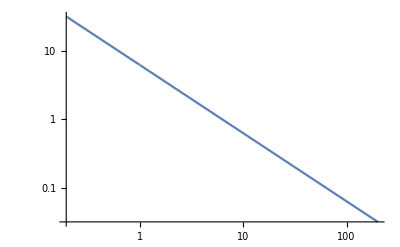

```mathematica
LogLogPlot[Abs[K[a*ω0]*G[a*ω0]],{a,0,200}]
```

```mathematica
LogLinearPlot[Arg[K[a*ω0]*G[a*ω0]],{a,0.01,200},PlotRange->Full]
```

-Graphics-